```mathematica
image=Import["/Users/calebmcwhorter/Desktop/curve.png"]
```

-Graphics-

```mathematica
newimage={};
Do[AppendTo[newimage,{}],{i,1,533}];

imdata=ImageData[image];

Do[
If[
imdata[[i,j]]=={1.,1.,1.,1.},
AppendTo[newimage[[i]],{1.,1.,1.,1.}],
AppendTo[newimage[[i]],{0.7215686274509804,0.01568627450980392,0.235294,0}]
],

{i,1,533},{j,1,767}
]
```

```mathematica
Sharpen[Image[newimage]]
```

-Graphics-

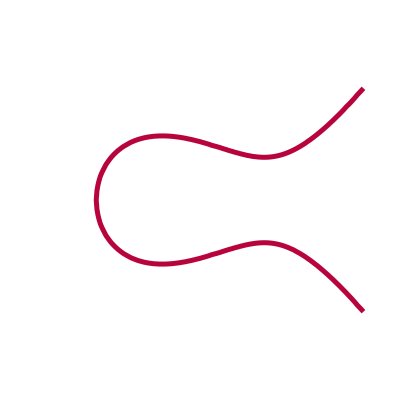

```mathematica
a=3;
b=1.7;
ContourPlot[
y^2==x^3-x+1
,{x,-2,b},{y,-a,a},
BaseStyle->{Thickness[0.009],RGBColor["#b8043c"]},Axes->False,Frame->False
]
```

```mathematica
10
```

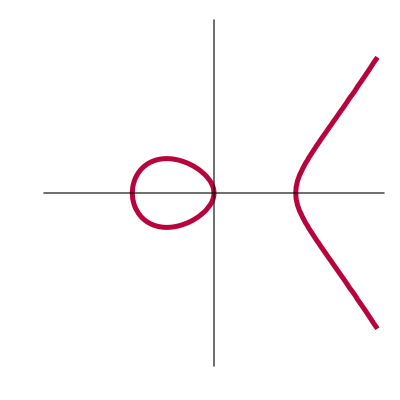

```mathematica
ContourPlot[
y^2==x(x^2-1)
,{x,-2,2},{y,-3,3},
Axes->True,Frame->False,Ticks->None,BaseStyle->{Thickness[0.009],RGBColor["#b8043c"]}
]
```

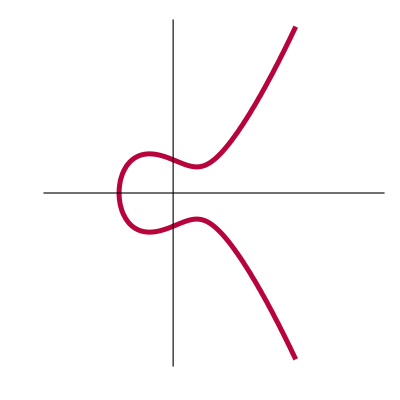

```mathematica
ContourPlot[
y^2==x^3-x+1
,{x,-3,5},{y,-5,5},
Axes->True,Frame->False,Ticks->None,BaseStyle->{Thickness[0.009],RGBColor["#b8043c"]}
]
```

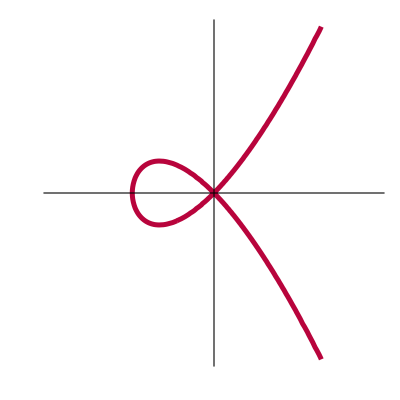

```mathematica
ContourPlot[
y^2==x^2(x+1)
,{x,-2,2},{y,-2,2},
Axes->True,Frame->False,Ticks->None,BaseStyle->{Thickness[0.009],RGBColor["#b8043c"]}
]
```

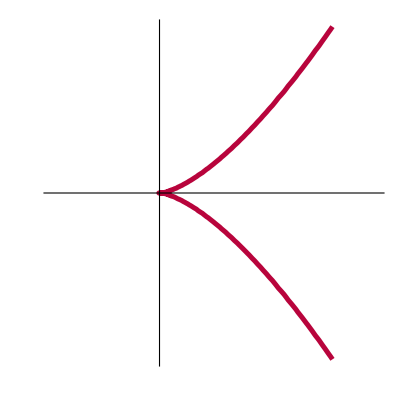

```mathematica
ContourPlot[
y^2==x^3
,{x,-1,2},{y,-2,2},
Axes->True,Frame->False,Ticks->None,BaseStyle->{Thickness[0.009],RGBColor["#b8043c"]}
]
```